# Transition Elements

## Preliminary Functions

The following function gives all Young tableaux’  with n boxes in form of lists (already defined in InvariantAlgebras.nb).

```mathematica
(*Clear[YTableaux]
YTableaux[a_] := IntegerPartitions[a]//Tableaux/@#&//Flatten[#,1]&*)
```

The following function give the row-word and column-word respectively of a Young tableaux (also defined in MOLDOperators.nb and not needed here).

```mathematica
(*Clear[RowWord,ColumnWord] 
RowWord[tableau_]:=tableau//Flatten
ColumnWord[tableau_]:=tableau//TransposeTableau//Flatten*)
```

It will be convenient to define an absolute value (in the regular sense). as the length of the vector.

```mathematica
Clear[AbsoluteValue]
AbsoluteValue[a_List]:=a//Power[#,2]&//Total;
AbsoluteValue[a_Complex]:=√(Re[a]^2+Im[a]^2);
AbsoluteValue[a_]:=√(a^2);
```

### Number of Projection Operators

Using the isomorphism between the Hermitean primitive invariants and the number of projection operators (for an n-particle algebra, irrespective how many of these n are particles, and how many are anti-particles!), we were able to obtain the following formula for the number of projection operators, and thus also the number of young tableaux of a given size: (Also defined in BlockStructure.nb)

```mathematica
Clear[NumberOfProjectionOps];

NumberOfProjectionOps[particles_]:=
NumberOfProjectionOps[particles]=Module[{},
1 + Sum[1/Factorial[j+1]*Product[Binomial[particles-2*l,2],{l,0,j}],{j,0,Floor[(particles-2)/2]}]
];
```

As an example, we calculate the number of Young tableaux consisting of 1,2,....,10 boxes.

```mathematica
Table[NumberOfProjectionOps[i],{i,1,10}]
```

{1,2,4,10,26,76,232,764,2620,9496}

### δδ-Functions into Coefficient vector

The following function called “δToCoefficientVector” transforms the δδ-function (as for example obtained through the function “PermutationTransitionElement”) into a coefficient vector of the corresponding algebra:

Each generic algebra-element α (where the algebra has dimension d) can be written as a linear combination of its basis elements e_i,
		α = (∑_(i=1))^d c_i e_i,
where the c_i are coefficients, c_1∈ Integers.
Therefore, one can define a corresponding coefficient vector, whose entries are the c_i in a canonical (as built in by Mathematica) order. For example, the coefficient vector corresponding to α is
		{c_1,c_2,... ,c_d}.
Since each permutation is a primitive invariant in and therefore also a basis element in it’s algebra, the corresponding coefficient vector will have entries 0 except for one place, where the entry is 1. For example, the 5^th basis element e_5 will have a coefficient vector
		{0,0,0,0,1,0, ... ,0}.
		
The first argument of the function “δToCoefficientVector” specifies the dimension d one wishes to view the permutation in, and the second argument is the δδ-function itself.The first line of the definition ensures that the function “δδToCoefficientVector”, if applied to a generic algebra-element, is applied to each of the basis elements separately. The second line ensures

```mathematica
ExplicitList[PermAlg[2]]
```

{δδ[a_1,b_1] δδ[a_2,b_2],δδ[a_1,b_2] δδ[a_2,b_1]}

```mathematica
Clear[δToCoefficientVector]

(*δToCoefficientVector[Algebra_[qdimension_,qbdimension___]][δδFunction_]:=Module[{},
δδFunction//Table[Coefficient[#,ExplicitList[Algebra[qdimension,qbdimension]][[i]]],{i,Dimension[Algebra[qdimension,qbdimension]]}]&]*)

δToCoefficientVector[Algebra_][δδFunction_]:=Module[{},
δδFunction//Table[Coefficient[#,ExplicitList[Algebra][[i]]],{i,Dimension[Algebra]}]&]
(*δδFunction/.Table[ExplicitList[PermAlg[dimension]][[i]]->Subscript[PermAlg[dimension], i],{i,Dimension[PermAlg[dimension]]}]//.Subscript[PermAlg[n_], a_]->a//Table[If[i==#,1,0],{i,Dimension[PermAlg[dimension]]}]&]*)
```

The following example calculates the coefficient-vector of several given algebra-elements

```mathematica
δToCoefficientVector[PermAlg[3]][δδ[Subscript[a, 1],Subscript[b, 1]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 2]]]
```

{0,1,0,0,0,0}

```mathematica
δToCoefficientVector[PermAlg[5]][δδ[Subscript[a, 1],Subscript[b, 1]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 2]] δδ[Subscript[a, 4],Subscript[b, 4]] δδ[Subscript[a, 5],Subscript[b, 5]]]
```

{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
δToCoefficientVector[PermAlg[3]][δδ[Subscript[a, 1],Subscript[b, 1]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 2]]+δδ[Subscript[a, 1],Subscript[b, 2]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 1]]]
```

{0,1,0,0,1,0}

```mathematica
δToCoefficientVector[PermAlg[3]][2*δδ[Subscript[a, 1],Subscript[b, 1]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 2]]+ 7*δδ[Subscript[a, 1],Subscript[b, 2]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 1]]]
```

{0,2,0,0,7,0}

```mathematica
δToCoefficientVector[PermAlg[3]][Nc*δδ[Subscript[a, 1],Subscript[b, 1]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 2]]+ 7*δδ[Subscript[a, 1],Subscript[b, 2]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 1]]]
```

{0,Nc,0,0,7,0}

```mathematica
δToCoefficientVector[PermAlg[3]][(Nc+2)/3*δδ[Subscript[a, 1],Subscript[b, 1]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 2]]+ 7*δδ[Subscript[a, 1],Subscript[b, 2]] δδ[Subscript[a, 2],Subscript[b, 3]] δδ[Subscript[a, 3],Subscript[b, 1]]]
```

{0,(2+Nc)/3,0,0,7,0}

#### δδ-Functions into Coefficient vector

We can now produce the inverse of the function “δToCoefficientVector”, namely “CoefficientVectorToδ”, which takes a coefficient vector as it’s argument and spits out the corresponding linear combination of δδ-functions. This is done via forming a dot product between the coefficient vector in question and the explicit form of the entire algebra, i.e. the vector containing all algebra elements in terms of δδ-functions.

```mathematica
Clear[CoefficientVectorToδ];
CoefficientVectorToδ[Algebra_][Coefficientvector_,A_:a,B_:b]:=Coefficientvector. ExplicitList[Algebra,A,B]
```

An Example

```mathematica
CoefficientVectorToδ[PermAlg[3]][{0,1,Nc/2,0,0,3}]
```

3 δδ[a_1,b_3] δδ[a_2,b_2] δδ[a_3,b_1]+δδ[a_1,b_1] δδ[a_2,b_3] δδ[a_3,b_2]+1/2 Nc δδ[a_1,b_2] δδ[a_2,b_1] δδ[a_3,b_3]

```mathematica
Clear[HermiteanConjugateδ]

HermiteanConjugateδ[δδFunction_,A_:a,B_:b]:=Module[{},
δδFunction//(#/.δδ[Subscript[A, aa_],Subscript[B, bb_]]:>δδ[Subscript[A, bb],Subscript[B, aa]])&
]
```

## Shape of a Young Tableau

The following function “TableauxShape” gives the shape of a list of lists, and thus also, more specifically, of aYoung tableau. The shape of a list of lists is defined to be the vectorwhose i^th entry is the length of the i^th list within the list. Therefore, the shape of a Young tableau is defined to be the vector whose i^th entry is the length of the i^th row of the Young tableau.

```mathematica
Clear[TableauxShape]
TableauxShape[a_List]:=Table[Length[a[[i]]],{i,Length[a]}]
```

Example: If we have the following Young tableaux with 5 boxes

```mathematica
YTableaux[5]//TableauGrid/@#&
```

{1 | 2 | 3 | 4 | 5,1 | 3 | 4 | 5
2 |  |  | ,1 | 2 | 4 | 5
3 |  |  | ,1 | 2 | 3 | 5
4 |  |  | ,1 | 2 | 3 | 4
5 |  |  | ,1 | 3 | 5
2 | 4 | ,1 | 2 | 5
3 | 4 | ,1 | 3 | 4
2 | 5 | ,1 | 2 | 4
3 | 5 | ,1 | 2 | 3
4 | 5 | ,1 | 4 | 5
2 |  | 
3 |  | ,1 | 3 | 5
2 |  | 
4 |  | ,1 | 2 | 5
3 |  | 
4 |  | ,1 | 3 | 4
2 |  | 
5 |  | ,1 | 2 | 4
3 |  | 
5 |  | ,1 | 2 | 3
4 |  | 
5 |  | ,1 | 4
2 | 5
3 | ,1 | 3
2 | 5
4 | ,1 | 2
3 | 5
4 | ,1 | 3
2 | 4
5 | ,1 | 2
3 | 4
5 | ,1 | 5
2 | 
3 | 
4 | ,1 | 4
2 | 
3 | 
5 | ,1 | 3
2 | 
4 | 
5 | ,1 | 2
3 | 
4 | 
5 | ,1
2
3
4
5}

Then, the shape of the third and seventh tableaux respectively are given by

```mathematica
TableauxShape[YTableaux[5][[3]]]
```

{4,1}

```mathematica
TableauxShape[YTableaux[5][[7]]]
```

{3,2}

The following function “TableauxShapeQ” tests whether two Young tableaux have the same shape

```mathematica
Clear[TableauxShapeQ]
TableauxShapeQ[dimension_,tableauxleft_,tableauxright_]:=Module[{ShapeTableauxLeft,ShapeTableauxRight},
ShapeTableauxLeft=TableauxShape[YTableaux[dimension][[tableauxleft]]];
ShapeTableauxRight=TableauxShape[YTableaux[dimension][[tableauxright]]];
If[ShapeTableauxRight==ShapeTableauxLeft,True,False]]
```

In the following example, it becomes clear that the second and third Young tableaux with 5 boxes have the same shape, however the second and seventh tableaux do not

```mathematica
TableauxShapeQ[5,2,3]
```

True

```mathematica
TableauxShapeQ[5,2,7]
```

False

## Hook-length, symmetrizer-count and normalization factors

In this section, we define a few basic quantities that are needed when working with Young tableaux. First, we define a function “HookLength” that, as the name suggests, calculates the Hook length h of a given Young tableaux. This is done via a built in function “Tableaux” from the Combinatorica package, which gives all possible Young tableaux of a certain shape. It should be noted that the Function “HookLength” takes a particular tableaux as input. On the other hand, The consecutively defined function “DiagramHookLength” merely takes a Young diagram (or shape of a Young tableaux) as input, as all tableaux of the same shape will have the same Hook length h, by definition.

```mathematica
Clear[HookLength];
HookLength[tableaux_]:=HookLength[tableaux]=Module[{},Factorial[tableaux//TableauxShape//Plus@@#&]/(tableaux//TableauxShape//Tableaux//Length)]
Clear[DiagramHookLength];
DiagramHookLength[diagram_]:=DiagramHookLength[diagram]=Module[{},Factorial[diagram//Plus@@#&]/(diagram//Tableaux//Length)]
```

To calculate the Normalization factor of a (Hermitean) Young projection operator corresponding to a particular tableaux (or even diagram, since this information is enough to obtain the normalization factor) one needs another quantity besides the hook-length. This quantity is in the literature often referred to as a_Y, see for example Cvitanovic: “Group Theory” (2008), and is defined as 
	a_Y= (∏_(i=1))^p|S_i|! (∏_(j=1))^q|A_q|!
where |S_k| and |A_k| are the length of the k^th symmetrizer and anti-symmetrizer respectively, and p and q are the total numbers of symmetrizers, resp. anti-symmetrizers, for the particular diagram.

```mathematica
Clear[SymASymCount];
SymASymCount[tableaux_]:=Module[{symcount,asymcount},
symcount=tableaux//Length/@#&//Factorial[#]&;
asymcount=tableaux//TransposeTableau//Length/@#&//Factorial[#]&;
Join[symcount,asymcount]//Times@@#&]
```

The function “TableauxNormalizationFactor” gives the normalization factor of a (Hermitean) Young projector corresponding to a particular tableaux. The normalization factor is simply given by
	a_y/h.

```mathematica
Clear[TableauxNormalizationFactor];
TableauxNormalizationFactor[tableaux_]:=Module[{},SymASymCount[tableaux]/HookLength[tableaux]]
```

## Transition Elements Permutation between Operators to obtain the Transition Element

```mathematica
(*Note that what follows is not yet written to work for qqbAlg as well as PermAlg - only PermAlg works so far*)
```

We found that the transition element between two operators projecting onto equivalent representations is given by the product of said two operators with a permutation between them, 
	T_ij=T_ii ρT_jj,
where T_ii and T_jj are projection operators, T_ij is the transition element between them and ρ is said permutation.

The following function “PermutationTransitionElement” calculates ρ for two given projection operators  T_ii and T_jj, or writes “No Transition Element” if the representations that  T_ii and T_jj project on are not equivalent.
The the permutation ρ is found in the following way: One forms the row-word for the two tableaux corresponding to the operators  T_ii and T_jj respectively. These two words will now be transformed into a product of δδ’s as follows: The  i^th δδ-function in the product will have the  i^th entry of the row-word of  T_ii as its first entry, and the  i^th entry of the row-word of  T_jj as its second entry. For example, if the row-words of  T_ii and T_jj are, respectively,
	{1,2,3} and {1,3,2},
then the product of δδ-functions will be
	δδ[a_1,b_1] δδ[a_2,b_3] δδ[a_3,b_2].
(This product will automatically be rearranged such that the first arguments of the δδ-functions appear in order in the product). 

The permutation found by “PermutationTransitionElement” can then be made into a birdtrack by using “δToBirdTrack”, as shown in the following two examples.

Note: The message “No Transition Element” is currently blocked out as it will be a nuisance in the later code.

```mathematica
Clear[PermutationTransitionElement]

PermutationTransitionElement[dimension_,operatorleft_,operatorright_]:=
PermutationTransitionElement[dimension,operatorleft,operatorright]=Module[{Wordleft,Wordright,ShapeOperatorLeft,ShapeOperatorRight},
ShapeOperatorLeft=TableauxShape[YTableaux[dimension][[operatorleft]]];
ShapeOperatorRight=TableauxShape[YTableaux[dimension][[operatorright]]];
Wordleft=YTableaux[dimension][[operatorleft]]//RowWord[#]&;
Wordright=YTableaux[dimension][[operatorright]]//RowWord[#]&;
If[Thread[ShapeOperatorLeft==ShapeOperatorRight],{Table[Subscript[a,Wordleft[[i]]],{i,Length[Wordleft]}],Table[Subscript[b,Wordright[[i]]],{i,Length[Wordright]}]}//Transpose//(Apply[δδ,#,{1}])&//(Times@@#&),0(*,Print["No Transition Element"]*)]]
```

Example: For 5 quarks, we now try to find ρ needed for a transition element between the first and the fifth operator and see that it does not exist, since these operators project onto inequivalent representations.
Furthermore, we try to find ρ needed for a transition element between the second and the third operator and find one below.

```mathematica
PermutationTransitionElement[5,1,5]
```

0

```mathematica
PermutationTransitionElement[5,2,3]
%//δToBirdTrack
```

δδ[a_1,b_1] δδ[a_2,b_3] δδ[a_3,b_2] δδ[a_4,b_4] δδ[a_5,b_5]

-Graphics-

## Transition Element in vector form

#### Shortened KS Transition Elements

The following function “TransitionElementVector” gives the transirion element between operatorleft and operatorright in terms of its coefficient vector (NOT SURE HOW THIS WORKS FOR YOUNGS - IT SHOUL NOT).
It should be noted that the function Vprod multiplies as
			“Vprod[a,b,c]=a*b*c”.

```mathematica
Clear[TransitionElementVector]

TransitionElementVector[dimension_,operatorleft_,operatorright_]:=Module[{OperatorLeftVec,OperatorRightVec,TransitionPermutation,TransitionElement},

OperatorLeftVec=YoungProjectorVec[YTableaux[dimension][[operatorleft]],dimension];
OperatorRightVec=YoungProjectorVec[YTableaux[dimension][[operatorright]],dimension];

TransitionPermutation=δToCoefficientVector[PermAlg[dimension]][PermutationTransitionElement[dimension,operatorleft,operatorright]];
TransitionElement=Vprod[PermAlg[dimension]][OperatorLeftVec,TransitionPermutation,OperatorRightVec];

TransitionElement
]
```

It should be noted that the Hermitean version of the above, “HermiteanTransitionElementVector” needs an extra prefactor to fulfill the required properties of a transition element. This pre-factor is found within the function “HermiteanTransitionElementVector”
	(“HermiteanTransitionElementVector” uses the KS-Operators)

```mathematica
Clear[HermiteanTransitionElementVector]

HermiteanTransitionElementVector[dimension_,operatorleft_,operatorright_]:=Module[{OperatorLeftVec,OperatorRightVec,TransitionPermutation,TransitionPermutationDag,TransitionElement,TransitionElementDag,normconstant,HermiteanNormFactor,TransitionOperator},

OperatorLeftVec=HermiteanYoungProjectorVec[YTableaux[dimension][[operatorleft]],dimension];
OperatorRightVec=HermiteanYoungProjectorVec[YTableaux[dimension][[operatorright]],dimension];

TransitionPermutation=δToCoefficientVector[PermAlg[dimension]][
PermutationTransitionElement[dimension,operatorleft,operatorright]];
TransitionElement=Vprod[PermAlg[dimension]][OperatorLeftVec,TransitionPermutation,OperatorRightVec];
TransitionPermutationDag=δToCoefficientVector[PermAlg[dimension]][PermutationTransitionElement[dimension,operatorright,operatorleft]];
TransitionElementDag= Vprod[PermAlg[dimension]][OperatorRightVec,TransitionPermutationDag,OperatorLeftVec];

If[TransitionElement==ConstantArray[0,TransitionElement//Length],ConstantArray[0,TransitionElement//Length],normconstant=Vprod[PermAlg[dimension]][TransitionElementDag,TransitionElement]-α*OperatorRightVec//(#==0)&/@#&//Solve[#,α]&;
HermiteanNormFactor=√(1/α)//(#/.normconstant//Flatten)&//(#/.{a_}:>a)&;
TransitionOperator=HermiteanNormFactor*TransitionElement;

TransitionOperator]
]
```

Let us consider the algebra of dimension 4.The following example calculates (in the following order)
	1.) The transition element T_79 between operators 7, P_7, and 9, P_9, in vector form
	2.) The product T_79 P_9 = T_79, as required
	3.) The product P_7 T_79 = T_79, as required
	4.) T_79^dagger T_79- P_9=0, as required
	5.)T_79 T_79^dagger- P_7=0, as required.
In steps 4.) and 5.), we used the fact that T^dagger is merely the transition element between P_9 and P_7, T_79^dagger=T_97.

```mathematica
TransitionElementVector[4,7,9]
%//Vprod[PermAlg[4]][#,YoungProjectorVec[YTableaux[4][[9]],4]]&
%%//Vprod[PermAlg[4]][YoungProjectorVec[YTableaux[4][[7]],4],#]&
Vprod[PermAlg[4]][TransitionElementVector[4,9,7],TransitionElementVector[4,7,9]]-YoungProjectorVec[YTableaux[4][[9]],4]
Vprod[PermAlg[4]][TransitionElementVector[4,7,9],TransitionElementVector[4,9,7]]-YoungProjectorVec[YTableaux[4][[7]],4]
```

{0,0,0,0,1/8,-1/8,1/8,-1/8,0,0,-1/8,1/8,-1/8,1/8,0,0,1/8,-1/8,1/8,-1/8,0,0,0,0}

{0,0,0,0,1/8,-1/8,1/8,-1/8,0,0,-1/8,1/8,-1/8,1/8,0,0,1/8,-1/8,1/8,-1/8,0,0,0,0}

{0,0,0,0,1/8,-1/8,1/8,-1/8,0,0,-1/8,1/8,-1/8,1/8,0,0,1/8,-1/8,1/8,-1/8,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Similarly for the Hermitean Young projectors and transition elements: We consider The the transition elements between  P_2, and P_3 (for 3 dimensions) in the following example. The example follows the exact same outline as the previous one.

```mathematica
HermiteanTransitionElementVector[3,2,3]
%//Vprod[PermAlg[3]][#,HermiteanYoungProjectorVec[YTableaux[3][[3]],3]]&
%%//Vprod[PermAlg[3]][HermiteanYoungProjectorVec[YTableaux[3][[2]],3],#]&
Vprod[PermAlg[3]][ HermiteanTransitionElementVector[3,3,2],HermiteanTransitionElementVector[3,2,3]]- HermiteanYoungProjectorVec[YTableaux[3][[3]],3]
Vprod[PermAlg[3]][ HermiteanTransitionElementVector[3,2,3],HermiteanTransitionElementVector[3,3,2]]- HermiteanYoungProjectorVec[YTableaux[3][[2]],3]
```

{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)}

{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)}

{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)}

{0,0,0,0,0,0}

{0,0,0,0,0,0}

#### MOLD Transition Elements (*Needs MOLDOperators.nb*)

We now wish to define the transition operators between MOLD operators. Before we dod this, we define the

Lastly, the function "MOLDTransitionElementVector" uses the MOLD operators. Thus, MOLDOperators.nb needs to have run. We need to manually normalize the MOLD transition operators - the appropriate normalization constant is found within the function “MOLDTransitionElementVector”.

```mathematica
Clear[MOLDTransitionElementVector]

MOLDTransitionElementVector[dimension_,operatorleft_,operatorright_]:=Module[{OperatorLeftVec,OperatorRightVec,TransitionPermutation,TransitionPermutationDag,TransitionElement,TransitionElementDag,normconstant,MOLDNormFactor,TransitionOperator},

OperatorLeftVec=MOLDProjectorVec[YTableaux[dimension][[operatorleft]],dimension];
OperatorRightVec=MOLDProjectorVec[YTableaux[dimension][[operatorright]],dimension];

TransitionPermutation=δToCoefficientVector[PermAlg[dimension]][PermutationTransitionElement[dimension,operatorleft,operatorright]];
TransitionElement=Vprod[PermAlg[dimension]][OperatorLeftVec,TransitionPermutation,OperatorRightVec];
TransitionPermutationDag=δToCoefficientVector[PermAlg[dimension]][PermutationTransitionElement[dimension,operatorright,operatorleft]];
TransitionElementDag= Vprod[PermAlg[dimension]][OperatorRightVec,TransitionPermutationDag,OperatorLeftVec];

If[TransitionElement==ConstantArray[0,TransitionElement//Length],ConstantArray[0,TransitionElement//Length],

normconstant=Vprod[PermAlg[dimension]][TransitionElementDag,TransitionElement]-α*OperatorRightVec//(#==0)&/@#&//Solve[#,α]&;
MOLDNormFactor=√(1/α)//(#/.normconstant//Flatten)&//(#/.{a_}:>a)&;
TransitionOperator=MOLDNormFactor*TransitionElement;

TransitionOperator]
]
```

We now consider the same example for the MOLD operators, as we did for the shortened KS-operators, and for the Young operators (should not work for Youngs...)

```mathematica
MOLDTransitionElementVector[3,2,3]
%//Vprod[PermAlg[3]][#,MOLDProjectorVec[YTableaux[3][[3]],3]]&
%%//Vprod[PermAlg[3]][MOLDProjectorVec[YTableaux[3][[2]],3],#]&
Vprod[PermAlg[3]][ MOLDTransitionElementVector[3,3,2],MOLDTransitionElementVector[3,2,3]]- MOLDProjectorVec[YTableaux[3][[3]],3]
Vprod[PermAlg[3]][MOLDTransitionElementVector[3,2,3],MOLDTransitionElementVector[3,3,2]]- MOLDProjectorVec[YTableaux[3][[2]],3]
```

{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)}

{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)}

{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)}

{0,0,0,0,0,0}

{0,0,0,0,0,0}

```mathematica
MOLDTransitionElementVector[4,7,9]
%//Vprod[PermAlg[4]][#,MOLDProjectorVec[YTableaux[4][[9]]]]&
%%//Vprod[PermAlg[4]][MOLDProjectorVec[YTableaux[4][[7]]],#]&
Vprod[PermAlg[4]][MOLDTransitionElementVector[4,9,7],MOLDTransitionElementVector[4,7,9]]-MOLDProjectorVec[YTableaux[4][[9]]]
Vprod[PermAlg[4]][MOLDTransitionElementVector[4,7,9],MOLDTransitionElementVector[4,9,7]]-MOLDProjectorVec[YTableaux[4][[7]]]
```

{0,0,0,0,1/(4 √6),-1/(4 √6),0,0,0,0,-1/(4 √6),1/(4 √6),0,0,0,0,1/(4 √6),-1/(4 √6),1/(4 √6),-1/(4 √6),-1/(4 √6),1/(4 √6),1/(4 √6),-1/(4 √6)}

{0,0,0,0,1/(4 √6),-1/(4 √6),0,0,0,0,-1/(4 √6),1/(4 √6),0,0,0,0,1/(4 √6),-1/(4 √6),1/(4 √6),-1/(4 √6),-1/(4 √6),1/(4 √6),1/(4 √6),-1/(4 √6)}

{0,0,0,0,1/(4 √6),-1/(4 √6),0,0,0,0,-1/(4 √6),1/(4 √6),0,0,0,0,1/(4 √6),-1/(4 √6),1/(4 √6),-1/(4 √6),-1/(4 √6),1/(4 √6),1/(4 √6),-1/(4 √6)}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The following transition operators are not properly normalized (this example gives the correct result, but the output is very large. This is why it was commented out).

```mathematica
(*MOLDTransitionElementVector[5,12,14]
%//Vprod[PermAlg[5]][MOLDProjectorVec[YTableaux[5][[14]]],#]&
%%//Vprod[PermAlg[5]][#,MOLDProjectorVec[YTableaux[5][[12]]]]&
Vprod[PermAlg[5]][MOLDTransitionElementVector[5,12,14],MOLDTransitionElementVector[5,14,12]]-MOLDProjectorVec[YTableaux[5][[14]]]
Vprod[PermAlg[5]][MOLDTransitionElementVector[5,14,12],MOLDTransitionElementVector[5,12,14]]-MOLDProjectorVec[YTableaux[5][[12]]]*)
```

### Table of all Transition Elements

The following function “HermiteanTransitionElemenVectArray” gives an array (or table) of all transition elements for a particular dimension (should not work for Youngs...).
The function first calculates all transition elements there are between all elements. Then, it deletes the transition elements between an operator and itself (which is done by removing the diagonal of the table, since the diagonal elements a_ii are the transition elements between operators P_i and P_i). Then, it removes all the zero vectors which stem from trying to find transition elements between operators projecting onto non-equivalent sub-algebras.
All transition elements are given in form of their component vectors

```mathematica
Clear[TransitionElementVecArray];

TransitionElementVecArray[dimension_]:=
TransitionElementVecArray[dimension]=Module[{transitionelementtable},
transitionelementtable=Table[Table[TransitionElementVector[dimension,j,i],{i,NumberOfTableaux[dimension]}],{j,NumberOfTableaux[dimension]}];
DeleteCases[transitionelementtable//Flatten[#,1]&,Alternatives@@Diagonal[transitionelementtable]]//DeleteCases[#,ConstantArray[0,Factorial[dimension]]]&]
```

```mathematica
Clear[HermiteanTransitionElementVecArray];

HermiteanTransitionElementVecArray[dimension_]:=
HermiteanTransitionElementVecArray[dimension]=Module[{transitionelementtable},

transitionelementtable=Table[Table[HermiteanTransitionElementVector[dimension,j,i],{i,NumberOfTableaux[dimension]}],{j,NumberOfTableaux[dimension]}];

DeleteCases[transitionelementtable//Flatten[#,1]&,Alternatives@@Diagonal[transitionelementtable]]//DeleteCases[#,ConstantArray[0,Factorial[dimension]]]&
]
```

And similarly for the MOLD operators.

```mathematica
Clear[MOLDTransitionElementVecArray];

MOLDTransitionElementVecArray[dimension_]:=
MOLDTransitionElementVecArray[dimension]=Module[{transitionelementtable,transitionelements},

transitionelementtable=Table[Table[MOLDTransitionElementVector[dimension,j,i],{i,NumberOfTableaux[dimension]}],{j,NumberOfTableaux[dimension]}];

transitionelements=DeleteCases[transitionelementtable//Flatten[#,1]&,Alternatives@@Diagonal[transitionelementtable]]//DeleteCases[#,ConstantArray[0,Factorial[dimension]]]&;

transitionelements
]
```

The following example illustrates that there are no transition elements in the algebra of 2 quarks, but there are two transition elements in the algebra of 3 quarks. This is done using the shortened KS operaotrs and the MOLD operators.

```mathematica
HermiteanTransitionElementVecArray[2]
MOLDTransitionElementVecArray[2]
```

Table::iterb: Iterator {j,NumberOfTableaux[2]} does not have appropriate bounds.

Table::iterb: Iterator {i,NumberOfTableaux[2]} does not have appropriate bounds.

Diagonal::list: List expected at position 1 in Diagonal[Table[Table[HermiteanTransitionElementVector[2,j,i],{i,NumberOfTableaux[2]}],{j,NumberOfTableaux[2]}]].

Table[HermiteanTransitionElementVector[2,j,i],{i,NumberOfTableaux[2]},{j,NumberOfTableaux[2]}]

Table::iterb: Iterator {j,NumberOfTableaux[2]} does not have appropriate bounds.

Table::iterb: Iterator {i,NumberOfTableaux[2]} does not have appropriate bounds.

Diagonal::list: List expected at position 1 in Diagonal[Table[Table[MOLDTransitionElementVector[2,j,i],{i,NumberOfTableaux[2]}],{j,NumberOfTableaux[2]}]].

Table[MOLDTransitionElementVector[2,j,i],{i,NumberOfTableaux[2]},{j,NumberOfTableaux[2]}]

```mathematica
HermiteanTransitionElementVecArray[3]
HermiteanTransitionElementVecArray[3]
HermiteanTransitionElementVector[3,2,3]
HermiteanTransitionElementVector[3,3,2]

MOLDTransitionElementVecArray[3]
MOLDTransitionElementVecArray[3]
MOLDTransitionElementVector[3,2,3]
MOLDTransitionElementVector[3,3,2]
```

{{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)},{0,1/(2 √3),0,1/(2 √3),-1/(2 √3),-1/(2 √3)}}

{{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)},{0,1/(2 √3),0,1/(2 √3),-1/(2 √3),-1/(2 √3)}}

{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)}

{0,1/(2 √3),0,1/(2 √3),-1/(2 √3),-1/(2 √3)}

{{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)},{0,1/(2 √3),0,1/(2 √3),-1/(2 √3),-1/(2 √3)}}

{{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)},{0,1/(2 √3),0,1/(2 √3),-1/(2 √3),-1/(2 √3)}}

{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)}

{0,1/(2 √3),0,1/(2 √3),-1/(2 √3),-1/(2 √3)}

## Full Algebra of Quarks

The following function “FullAlgebraVec” gives a list of all Young projection operators and transition elements for a particular dimension (since they should not exist, this function is commented out.
The function “FullHermiteanAlgebraVec” gives a list of all Hermitean Young projection operators and corresponding  transition elements for a particular dimension.
The function “FullMOLDAlgebraVec” gives a list of all Hermitean Young projection operators and corresponding  transition elements constructed using MOLD, for a particular dimension.

For these functions to work, the notebook MOLDOperators.nb needs to have run.

```mathematica
(*Clear[FullAlgebraVec];

FullAlgebraVec[dimension_]:=FullAlgebraVec[dimension]=Join[Table[YoungProjectorVec[YTableaux[dimension][[i]],dimension],{i,NumberOfTableaux[dimension]}],TransitionElementVecArray[dimension]];*)
```

```mathematica
Clear[FullHermiteanAlgebraVec, FullMOLDAlgebraVec];

FullHermiteanAlgebraVec[dimension_]:=FullHermiteanAlgebraVec[dimension]=Join[Table[HermiteanYoungProjectorVec[YTableaux[dimension][[i]],dimension],{i,NumberOfTableaux[dimension]}],HermiteanTransitionElementVecArray[dimension]];

FullMOLDAlgebraVec[dimension_]:=FullMOLDAlgebraVec[dimension]=Join[Table[MOLDProjectorVec[YTableaux[dimension][[i]],dimension],{i,NumberOfTableaux[dimension]}],MOLDTransitionElementVecArray[dimension]];
```

The following example gives the Hermitean algebra for dimensions 2 (both shortened KS and MOLD), 3, and 4 (MOLD only). We also calulated the length of these vectors to demonstrate that, for a given dimension d, the corresponding algebra is indeed d!-dimensional.

```mathematica
FullHermiteanAlgebraVec[2]
%//Length
FullMOLDAlgebraVec[2]
%//Length
```

Table::iterb: Iterator {i,NumberOfTableaux[2]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[HermiteanYoungProjectorVec[YTableaux[2]⟦i⟧,2],{i,NumberOfTableaux[2]},{HermiteanTransitionElementVector[2,j,i]},{i,NumberOfTableaux[2]},{j,NumberOfTableaux[2]}]

Table::iterb: Iterator {i,NumberOfTableaux[2]} does not have appropriate bounds.

5

Table::iterb: Iterator {i,NumberOfTableaux[2]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[MOLDProjectorVec[YTableaux[2]⟦i⟧,2],{i,NumberOfTableaux[2]},{MOLDTransitionElementVector[2,j,i]},{i,NumberOfTableaux[2]},{j,NumberOfTableaux[2]}]

5

```mathematica
FullMOLDAlgebraVec[3]
%//Length
```

{{1/6,1/6,1/6,1/6,1/6,1/6},{1/3,1/6,-1/3,-1/6,-1/6,1/6},{1/3,-1/6,1/3,-1/6,-1/6,-1/6},{1/6,-1/6,-1/6,1/6,1/6,-1/6},{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)},{0,1/(2 √3),0,1/(2 √3),-1/(2 √3),-1/(2 √3)}}

6

Below, we have calculated the product of all pairs of the 4q-algebra in the multiplet basis. We have then re-ordered the basis to make the block-structure of the multiplication table much more explicit.

Table::iterb: Iterator {i,NumberOfTableaux[4]} does not have appropriate bounds.

Table::iterb: Iterator {j,NumberOfTableaux[4]} does not have appropriate bounds.

Table::iterb: Iterator {i,NumberOfTableaux[4]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Diagonal::list: List expected at position 1 in Diagonal[Table[Table[MOLDTransitionElementVector[4,j,i],{i,NumberOfTableaux[4]}],{j,NumberOfTableaux[4]}]].

5

Table::iterb: Iterator {i,NumberOfTableaux[4]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partw: Part 3 of YTableaux[4] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

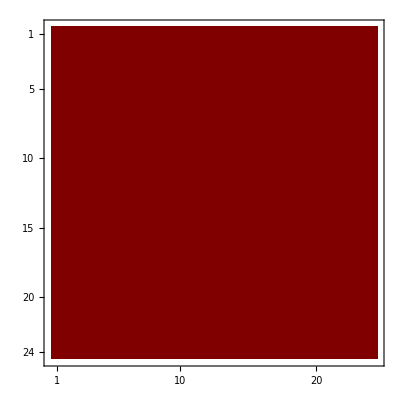

Part::pkspec1: The expression i cannot be used as a part specification.

Part::partw: Part 11 of Table[MOLDProjectorVec[YTableaux[4]⟦i⟧,4],{i,NumberOfTableaux[4]},{MOLDTransitionElementVector[4,j,i]},{i,NumberOfTableaux[4]},{j,NumberOfTableaux[4]}] does not exist.

Part::partw: Part 12 of Table[MOLDProjectorVec[YTableaux[4]⟦i⟧,4],{i,NumberOfTableaux[4]},{MOLDTransitionElementVector[4,j,i]},{i,NumberOfTableaux[4]},{j,NumberOfTableaux[4]}] does not exist.

Part::partw: Part 13 of Table[MOLDProjectorVec[YTableaux[4]⟦i⟧,4],{i,NumberOfTableaux[4]},{MOLDTransitionElementVector[4,j,i]},{i,NumberOfTableaux[4]},{j,NumberOfTableaux[4]}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Table::iterb: Iterator {i,Dimension[PermAlg[4]]} does not have appropriate bounds.

Table::iterb: Iterator {i,NumberOfTableaux[4]} does not have appropriate bounds.

Part::partw: Part 11 of Table[MOLDProjectorVec[YTableaux[4]⟦i⟧,4],{i,NumberOfTableaux[4]},{MOLDTransitionElementVector[4,j,i]},{i,NumberOfTableaux[4]},{j,NumberOfTableaux[4]}] does not exist.

Part::partw: Part 12 of Table[MOLDProjectorVec[YTableaux[4]⟦i⟧,4],{i,NumberOfTableaux[4]},{MOLDTransitionElementVector[4,j,i]},{i,NumberOfTableaux[4]},{j,NumberOfTableaux[4]}] does not exist.

Part::partw: Part 13 of Table[MOLDProjectorVec[YTableaux[4]⟦i⟧,4],{i,NumberOfTableaux[4]},{MOLDTransitionElementVector[4,j,i]},{i,NumberOfTableaux[4]},{j,NumberOfTableaux[4]}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {i,Dimension[PermAlg[4]]} does not have appropriate bounds.

Table::iterb: Iterator {i,NumberOfTableaux[4]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
FullMOLDAlgebraVec[4];
%//Length
%%//Table[Table[Vprod[PermAlg[4]][#[[i]],#[[j]]]//Power[#,2]&//Total,{j,1,24}],{i,1,24}]&//MatrixPlot
ReorderFullMOLDAlgebra[4]=FullMOLDAlgebraVec[4]//{#[[1]],#[[2]],#[[11]],#[[12]],#[[13]],#[[3]],#[[14]],#[[15]],#[[16]],#[[4]],#[[5]],#[[17]],#[[18]],#[[6]],#[[7]],#[[19]],#[[20]],#[[21]],#[[8]],#[[22]],#[[23]],#[[24]],#[[9]],#[[10]]}&;
%//Table[Table[Vprod[PermAlg[4]][#[[i]],#[[j]]]//Power[#,2]&//Total,{j,1,24}],{i,1,24}]&//MatrixPlot
(*%//Export["Multiplicaton4qMultipletBasis.eps",#]&*)
```

### Tha Algebra as a Matrix

The function “Full***AlgebraMatrix” return the matrix of the algebra of n particles. This matrix is arranged such that each diagonal element m_ii is a projection operator, and each off-diagonal element m_ij is a transition operator between m_ii and m_jj.

```mathematica
Clear[FullHermiteanAlgebraMatrix,FullMOLDAlgebraMatrix]

FullHermiteanAlgebraMatrix[dimension_]:=
FullHermiteanAlgebraMatrix[dimension]=Module[{},
Table[Table[HermiteanTransitionElementVector[dimension,i,j],{j,1,NumberOfProjectionOps[dimension]}],{i,1,NumberOfProjectionOps[dimension]}]
]

FullMOLDAlgebraMatrix[dimension_]:=
FullMOLDAlgebraMatrix[dimension]=Module[{},
Table[Table[MOLDTransitionElementVector[dimension,i,j],{j,1,NumberOfProjectionOps[dimension]}],{i,1,NumberOfProjectionOps[dimension]}]
]
```

As an example, we find the MOLD-algebra for 3 quarks.

```mathematica
FullMOLDAlgebraMatrix[4]//MatrixForm
```

((1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24
1/24) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (1/8
1/8
1/16
1/16
1/16
1/16
-1/8
-1/8
-1/16
-1/16
-1/16
-1/16
-1/16
-1/16
1/16
1/16
0
0
-1/16
-1/16
1/16
1/16
0
0) | (0
0
(√3)/16
1/(16 √3)
(√3)/16
1/(16 √3)
0
0
-(√3)/16
-1/(16 √3)
-(√3)/16
-1/(16 √3)
(√3)/16
1/(16 √3)
-(√3)/16
-1/(16 √3)
-1/(8 √3)
1/(8 √3)
(√3)/16
1/(16 √3)
-(√3)/16
-1/(16 √3)
-1/(8 √3)
1/(8 √3)) | (0
0
0
1/(4 √6)
0
1/(4 √6)
0
0
0
-1/(4 √6)
0
-1/(4 √6)
0
1/(4 √6)
0
-1/(4 √6)
1/(4 √6)
-1/(4 √6)
0
1/(4 √6)
0
-1/(4 √6)
1/(4 √6)
-1/(4 √6)) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
(√3)/16
(√3)/16
1/(16 √3)
1/(16 √3)
0
0
(√3)/16
(√3)/16
1/(16 √3)
1/(16 √3)
-(√3)/16
-(√3)/16
-(√3)/16
-(√3)/16
-1/(8 √3)
-1/(8 √3)
-1/(16 √3)
-1/(16 √3)
-1/(16 √3)
-1/(16 √3)
1/(8 √3)
1/(8 √3)) | (1/8
1/24
-1/16
-1/48
-1/48
5/48
1/8
1/24
-1/16
-1/48
-1/48
5/48
-1/16
-1/48
-1/16
-1/48
-1/12
-1/12
-1/48
5/48
-1/48
5/48
-1/12
-1/12) | (0
1/(6 √2)
0
-1/(12 √2)
1/(6 √2)
-1/(12 √2)
0
1/(6 √2)
0
-1/(12 √2)
1/(6 √2)
-1/(12 √2)
0
-1/(12 √2)
0
-1/(12 √2)
-1/(12 √2)
-1/(12 √2)
1/(6 √2)
-1/(12 √2)
1/(6 √2)
-1/(12 √2)
-1/(12 √2)
-1/(12 √2)) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
1/(4 √6)
1/(4 √6)
0
0
0
0
1/(4 √6)
1/(4 √6)
0
0
0
0
1/(4 √6)
1/(4 √6)
-1/(4 √6)
-1/(4 √6)
-1/(4 √6)
-1/(4 √6)
-1/(4 √6)
-1/(4 √6)) | (0
1/(6 √2)
0
1/(6 √2)
-1/(12 √2)
-1/(12 √2)
0
1/(6 √2)
0
1/(6 √2)
-1/(12 √2)
-1/(12 √2)
0
1/(6 √2)
0
1/(6 √2)
-1/(12 √2)
-1/(12 √2)
-1/(12 √2)
-1/(12 √2)
-1/(12 √2)
-1/(12 √2)
-1/(12 √2)
-1/(12 √2)) | (1/8
-1/24
1/8
-1/24
-1/24
-1/24
1/8
-1/24
1/8
-1/24
-1/24
-1/24
1/8
-1/24
1/8
-1/24
-1/24
-1/24
-1/24
-1/24
-1/24
-1/24
-1/24
-1/24) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (1/12
-1/12
1/24
-1/24
-1/24
1/24
-1/12
1/12
-1/24
1/24
1/24
-1/24
-1/24
1/24
1/24
-1/24
1/12
-1/12
1/24
-1/24
-1/24
1/24
-1/12
1/12) | (0
0
1/(8 √3)
1/(8 √3)
-1/(8 √3)
-1/(8 √3)
0
0
-1/(8 √3)
-1/(8 √3)
1/(8 √3)
1/(8 √3)
1/(8 √3)
1/(8 √3)
-1/(8 √3)
-1/(8 √3)
0
0
-1/(8 √3)
-1/(8 √3)
1/(8 √3)
1/(8 √3)
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
1/(8 √3)
-1/(8 √3)
1/(8 √3)
-1/(8 √3)
0
0
1/(8 √3)
-1/(8 √3)
1/(8 √3)
-1/(8 √3)
-1/(8 √3)
1/(8 √3)
-1/(8 √3)
1/(8 √3)
0
0
-1/(8 √3)
1/(8 √3)
-1/(8 √3)
1/(8 √3)
0
0) | (1/12
1/12
-1/24
-1/24
-1/24
-1/24
1/12
1/12
-1/24
-1/24
-1/24
-1/24
-1/24
-1/24
-1/24
-1/24
1/12
1/12
-1/24
-1/24
-1/24
-1/24
1/12
1/12) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (1/8
1/24
-1/8
-1/24
-1/24
1/24
-1/8
-1/24
1/8
1/24
1/24
-1/24
1/8
1/24
-1/8
-1/24
-1/24
1/24
1/24
-1/24
-1/24
1/24
1/24
-1/24) | (0
1/(6 √2)
0
-1/(6 √2)
1/(12 √2)
-1/(12 √2)
0
-1/(6 √2)
0
1/(6 √2)
-1/(12 √2)
1/(12 √2)
0
1/(6 √2)
0
-1/(6 √2)
1/(12 √2)
-1/(12 √2)
-1/(12 √2)
1/(12 √2)
1/(12 √2)
-1/(12 √2)
-1/(12 √2)
1/(12 √2)) | (0
0
0
0
1/(4 √6)
-1/(4 √6)
0
0
0
0
-1/(4 √6)
1/(4 √6)
0
0
0
0
1/(4 √6)
-1/(4 √6)
1/(4 √6)
-1/(4 √6)
-1/(4 √6)
1/(4 √6)
1/(4 √6)
-1/(4 √6)) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
1/(6 √2)
0
1/(12 √2)
-1/(6 √2)
-1/(12 √2)
0
-1/(6 √2)
0
-1/(12 √2)
1/(6 √2)
1/(12 √2)
0
-1/(12 √2)
0
1/(12 √2)
1/(12 √2)
-1/(12 √2)
1/(6 √2)
1/(12 √2)
-1/(6 √2)
-1/(12 √2)
-1/(12 √2)
1/(12 √2)) | (1/8
-1/24
1/16
-1/48
-1/48
-5/48
-1/8
1/24
-1/16
1/48
1/48
5/48
-1/16
1/48
1/16
-1/48
-1/12
1/12
1/48
5/48
-1/48
-5/48
1/12
-1/12) | (0
0
(√3)/16
-(√3)/16
-1/(16 √3)
1/(16 √3)
0
0
-(√3)/16
(√3)/16
1/(16 √3)
-1/(16 √3)
(√3)/16
-(√3)/16
-(√3)/16
(√3)/16
1/(8 √3)
-1/(8 √3)
-1/(16 √3)
1/(16 √3)
1/(16 √3)
-1/(16 √3)
1/(8 √3)
-1/(8 √3)) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
1/(4 √6)
0
-1/(4 √6)
0
0
0
1/(4 √6)
0
-1/(4 √6)
0
-1/(4 √6)
0
-1/(4 √6)
1/(4 √6)
1/(4 √6)
0
1/(4 √6)
0
1/(4 √6)
-1/(4 √6)
-1/(4 √6)) | (0
0
(√3)/16
-1/(16 √3)
-(√3)/16
1/(16 √3)
0
0
(√3)/16
-1/(16 √3)
-(√3)/16
1/(16 √3)
-(√3)/16
1/(16 √3)
-(√3)/16
1/(16 √3)
1/(8 √3)
1/(8 √3)
(√3)/16
-1/(16 √3)
(√3)/16
-1/(16 √3)
-1/(8 √3)
-1/(8 √3)) | (1/8
-1/8
-1/16
1/16
1/16
-1/16
1/8
-1/8
-1/16
1/16
1/16
-1/16
-1/16
1/16
-1/16
1/16
0
0
1/16
-1/16
1/16
-1/16
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (1/24
-1/24
-1/24
1/24
1/24
-1/24
-1/24
1/24
1/24
-1/24
-1/24
1/24
1/24
-1/24
-1/24
1/24
1/24
-1/24
-1/24
1/24
1/24
-1/24
-1/24
1/24))

```mathematica
FullMOLDAlgebraMatrix[3]//MatrixForm
```

((1/6
1/6
1/6
1/6
1/6
1/6) | (0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
0
0
0
0
0)
(0
0
0
0
0
0) | (1/3
1/6
-1/3
-1/6
-1/6
1/6) | (0
1/(2 √3)
0
-1/(2 √3)
1/(2 √3)
-1/(2 √3)) | (0
0
0
0
0
0)
(0
0
0
0
0
0) | (0
1/(2 √3)
0
1/(2 √3)
-1/(2 √3)
-1/(2 √3)) | (1/3
-1/6
1/3
-1/6
-1/6
-1/6) | (0
0
0
0
0
0)
(0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
0
0
0
0
0) | (1/6
-1/6
-1/6
1/6
1/6
-1/6))

```mathematica
FullMOLDAlgebraMatrix[3]//Flatten[#,1]&//DeleteCases[#,ConstantArray[0,6]]&
%//Vprod[PermAlg[3]][#[[3]],#[[2]]]&
%%//Table[Table[Vprod[PermAlg[3]][#[[i]],#[[j]]],{i,1,6}],{j,1,6}]&//MatrixForm
```

{{1/6,1/6,1/6,1/6,1/6,1/6},{1/3,1/6,-1/3,-1/6,-1/6,1/6},{0,1/(2 √3),0,-1/(2 √3),1/(2 √3),-1/(2 √3)},{0,1/(2 √3),0,1/(2 √3),-1/(2 √3),-1/(2 √3)},{1/3,-1/6,1/3,-1/6,-1/6,-1/6},{1/6,-1/6,-1/6,1/6,1/6,-1/6}}

{0,0,0,0,0,0}

((1/6
1/6
1/6
1/6
1/6
1/6) | (0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
0
0
0
0
0)
(0
0
0
0
0
0) | (1/3
1/6
-1/3
-1/6
-1/6
1/6) | (0
0
0
0
0
0) | (0
1/(2 √3)
0
1/(2 √3)
-1/(2 √3)
-1/(2 √3)) | (0
0
0
0
0
0) | (0
0
0
0
0
0)
(0
0
0
0
0
0) | (0
1/(2 √3)
0
-1/(2 √3)
1/(2 √3)
-1/(2 √3)) | (0
0
0
0
0
0) | (1/3
-1/6
1/3
-1/6
-1/6
-1/6) | (0
0
0
0
0
0) | (0
0
0
0
0
0)
(0
0
0
0
0
0) | (0
0
0
0
0
0) | (1/3
1/6
-1/3
-1/6
-1/6
1/6) | (0
0
0
0
0
0) | (0
1/(2 √3)
0
1/(2 √3)
-1/(2 √3)
-1/(2 √3)) | (0
0
0
0
0
0)
(0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
1/(2 √3)
0
-1/(2 √3)
1/(2 √3)
-1/(2 √3)) | (0
0
0
0
0
0) | (1/3
-1/6
1/3
-1/6
-1/6
-1/6) | (0
0
0
0
0
0)
(0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
0
0
0
0
0) | (0
0
0
0
0
0) | (1/6
-1/6
-1/6
1/6
1/6
-1/6))

The next example is commented out due to the large output, but works well.

```mathematica
(*FullMOLDAlgebraMatrix[5]//MatrixForm
(*%//Export["5FullMOLDAlgebraMatrix.pdf",#]&*)*)
```

### Block-Structure

Th function “BlockStructure” calculates the block-structure of the nq-algebra by comparing shapes of Young tableaux. The functions “***BlockStructure” give the block structure via calculate the absolute value of each of the vectors of “Full***AlgebraMatrix” first - this is naturally much slower than “BlockStructure”, but it also works. Further, it is a nice way to check whether “Full***AlgebraMatrix” gives the correct answer.

```mathematica
Clear[BlockStructure,HermiteanBlockStructure,MOLDBlockStructure]

BlockStructure[dimension_]:=Module[{},
Table[Table[If[TableauxShapeQ[dimension,i,j],(*TableauxShape[YTableaux[dimension][[i]]]//AbsoluteValue*)1,0],{j,1,YTableaux[dimension]//Length}],{i,1,YTableaux[dimension]//Length}]//MatrixPlot
]

HermiteanBlockStructure[dimension_]:=
HermiteanBlockStructure[dimension]=Module[{},
Table[Table[TransitionElementVector[dimension,i,j]//AbsoluteValue,{j,1,NumberOfProjectionOps[dimension]}],{i,1,NumberOfProjectionOps[dimension]}]//MatrixPlot
]

MOLDBlockStructure[dimension_]:=
MOLDBlockStructure[dimension]=Module[{},
Table[Table[MOLDTransitionElementVector[dimension,i,j]//AbsoluteValue,{j,1,NumberOfProjectionOps[dimension]}],{i,1,NumberOfProjectionOps[dimension]}]//MatrixPlot
]
```

We expose the matrix structure of the 5q-algebra using “BlockStructure”

{1 | 2 | 3 | 4 | 5,1 | 3 | 4 | 5
2 |  |  | ,1 | 2 | 4 | 5
3 |  |  | ,1 | 2 | 3 | 5
4 |  |  | ,1 | 2 | 3 | 4
5 |  |  | ,1 | 3 | 5
2 | 4 | ,1 | 2 | 5
3 | 4 | ,1 | 3 | 4
2 | 5 | ,1 | 2 | 4
3 | 5 | ,1 | 2 | 3
4 | 5 | ,1 | 4 | 5
2 |  | 
3 |  | ,1 | 3 | 5
2 |  | 
4 |  | ,1 | 2 | 5
3 |  | 
4 |  | ,1 | 3 | 4
2 |  | 
5 |  | ,1 | 2 | 4
3 |  | 
5 |  | ,1 | 2 | 3
4 |  | 
5 |  | ,1 | 4
2 | 5
3 | ,1 | 3
2 | 5
4 | ,1 | 2
3 | 5
4 | ,1 | 3
2 | 4
5 | ,1 | 2
3 | 4
5 | ,1 | 5
2 | 
3 | 
4 | ,1 | 4
2 | 
3 | 
5 | ,1 | 3
2 | 
4 | 
5 | ,1 | 2
3 | 
4 | 
5 | ,1
2
3
4
5}

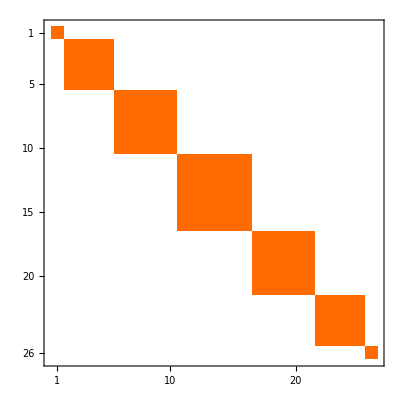

```mathematica
YTableaux[5];
%//TableauGrid/@#&
BlockStructure[5]
(*%//Export["5MOLDBlockStructure.pdf",#]&*)
```

We expose the matrix structure of the 3q- and the 4q-algebras using both the KS operators and the MOLD operators. (This example is commented out because it takes long, but it works very well)

```mathematica
(*HermiteanBlockStructure[3]
MOLDBlockStructure[3]
HermiteanBlockStructure[4]*)
MOLDBlockStructure[4]
(*%//Export["4MOLDBlockStructure.pdf",#]&*)
```

$Aborted

#### Form of block structure

Sometimes, we would like to know the block-structure of the algebra as a vector. For example, for the 3q-Algebra, we would like to have a vector {1,2,1}, and for the 4q-algebra a vector {1,3,2,3,1}. The following function “BlockStructureVector” gives this vector.

```mathematica
Clear[BlockStructureVector]

BlockStructureVector[2]={1,1};

BlockStructureVector[dimension_]:=
BlockStructureVector[dimension]=Module[{blockmatrix,blockvector},
blockmatrix=Table[Table[If[TableauxShapeQ[dimension,i,j],(*TableauxShape[YTableaux[dimension][[i]]]//AbsoluteValue*)1,0],{j,1,YTableaux[dimension]//Length}],{i,1,YTableaux[dimension]//Length}];
blockvector=blockmatrix//(#//.{xx___,a_List,b_List,yy___}:>{xx,a,yy}/;a==b)&//AbsoluteValue/@#&
]
```

As an example, we obtain the block-structure of the algebras from 1 to 7 quarks. We have compared the number of blocks with the number of partitions (as these clearly should be equal), to make sure, that we obtain the correct number of blocks

```mathematica
Table[BlockStructureVector[i],{i,1,7}]//MatrixForm
Table[BlockStructureVector[i]//Length,{i,1,7}]//MatrixForm
Table[NumberOfPartitions[i],{i,1,7}]//MatrixForm
```

Part::partw: Part 2 of {1} does not exist.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression 1+{}⟦1,1⟧ cannot be used as a part specification.

Last::nolast: {} has zero length and no last element.

Set::shape: Lists {Combinatorica`Private`row$437966} and Last[{}] are not the same shape.

Part::pkspec1: The expression Combinatorica`Private`row$437966 cannot be used as a part specification.

Set::pkspec1: The expression Combinatorica`Private`row$437966 cannot be used as a part specification.

({1}
{1,1}
{1,2,1}
{1,3,2,3,1}
{1,4,5,6,5,4,1}
{1,5,9,10,5,16,10,5,9,5,1}
{1,6,14,15,14,35,20,21,21,35,15,14,14,6,1})

(1
2
3
5
7
11
15)

(1
2
3
5
7
11
15)